# MMA 绘图系统学习

### 纯函数绘图

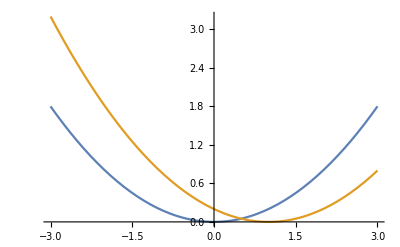

```mathematica
f = Function[x, 0.2x^2];
Plot[{f[t], f[t-1]}, {t, -3, 3}, AxesStyle->Arrowheads[{0,0.03}]]
```

### 模式匹配 + 延时赋值

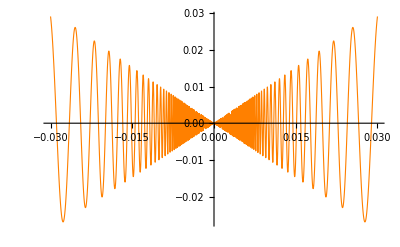

```mathematica
g3[x_] := x*Sin[1/x] + x^2;
Plot[g3[x], {x, -0.03, 0.03}, PlotStyle->{Thickness[0.002], Orange}]
```

## 3. 分段函数绘制

备注： /; 表是条件限制

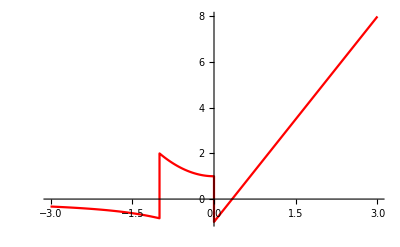

```mathematica
(*4.绘制一个分段函数g(x)*)

g[x_] := 3x-1/;x>0
g[x_] := x^2+1/;(x>=-1)&&(x<=0)
g[x_] := Sin[1/x]/;x<-1
Plot[g[t], {t, -3, 3}, PlotStyle->{Red}, PlotPoints->1000]
```

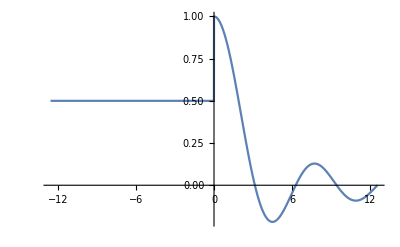

```mathematica
(*绘制分段函数的一个例子：Piecewisw[]函数*)
Clear[x];
f = Piecewise[{{0.5, x<=0}, {Sin[x]/x, x!=0}}];
Plot[f, {x, -4Pi, 4Pi}]
```

## 5. 三维图绘制

### 5.1 普通情况

```mathematica
Plot3D[Sin[x y], {x, -3, 3}, {y, -1, 1}]
```

-Graphics3D-

### 5.4 复变函数可视化

```mathematica
ComplexPlot3D[(z^2+1)/(z^2-1),{z,-2-2 I,2+2 I},PlotLegends->Automatic,AxesStyle->Arrowheads[{0,0.03}]]
```

-Graphics3D-

### 5.5 三维参数方程

```mathematica
ParametricPlot3D[{1.16^v*Cos[v]*(1+Cos[u]), -1.16^v*Sin[v]*(1+Cos[u]), -2 1.16^v*(1+Sin[u])},
	{u,0,2 Pi},{v,-15,6},
	Mesh->None,
	PlotStyle->{Opacity[0.6],Red},
	PlotRange->All,
	PlotPoints->25,
	Axes->False,
	Boxed->False]
```

-Graphics3D-

### 3.1 散点图绘制

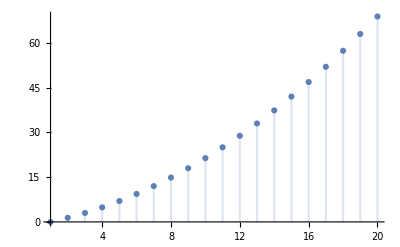

```mathematica
DiscretePlot[-1.125 + n + 0.125*n^2, {n, 1, 20}]
```

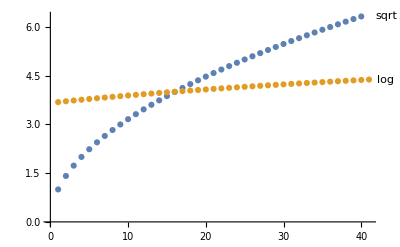

```mathematica
ListPlot[{Labeled[Sqrt[Range[40]],"sqrt"],Labeled[Log[Range[40,80]],"log"]}]
```

### 3.2 对数坐标

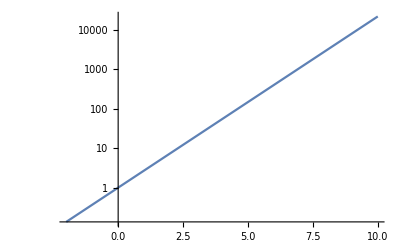

```mathematica
LogPlot[Exp[x], {x, -2, 10}]
```

### 4.4 参数方程绘制

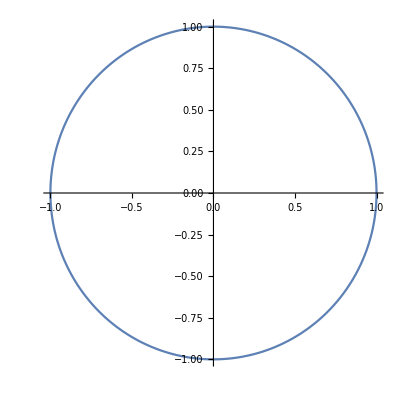

```mathematica
ParametricPlot[{Sin[t], Cos[t]}, {t, 0, 2Pi}]
```

### 图形填充

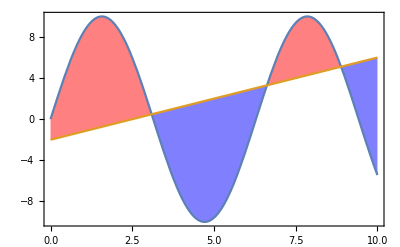

```mathematica
f=10 Sin[x];g=-2+0.8 x;
Plot[{f,g},{x,0,10},Filling->{1->{{2},{Lighter[Blue,0.5],Lighter[Red,0.5]}}},Frame->True]
```

## PlotRange + AxesStyle

1. 没有进行任何的设置时

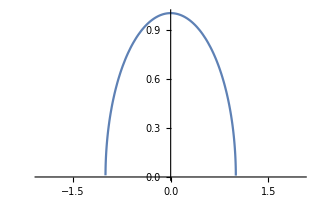

```mathematica
Plot[Sqrt[1-x^2], {x, -2, 2}]
```

2. 进行比列设置
这里的 比例 = 图形高度/图形宽度  

其中显函数的宽度和定义域有关， 隐函数的宽度就是实际指定的范围

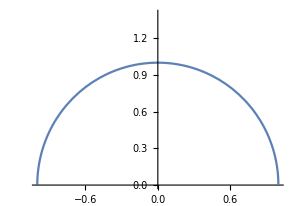

```mathematica
Plot[Sqrt[1-x^2], 
	{x, -1.2, 1.5},
	PlotRange->{0, 1.4},
	AspectRatio->1.4/(1+1)
]
```

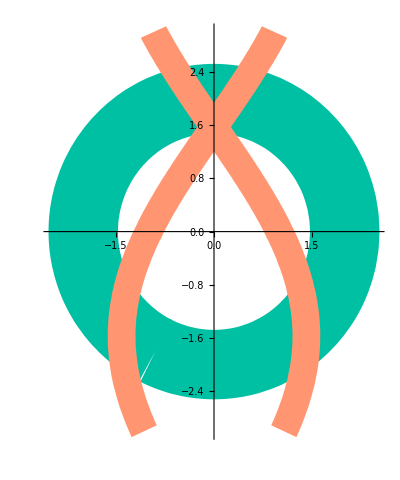

```mathematica
fp1 = ContourPlot[x^2 + y^2 == 4, {x, -1.3, 0.6}, {y, -2.4, 3.2}, AspectRatio->(2.4+3.2)/(1.3+0.6), ContourStyle->Red];
fp2 = ContourPlot[x^2 + y^2 == 4, {x, -3, 3}, {y, -3, 3}, AspectRatio->1, ContourStyle->RGBColor["#00C0A3"], AxesOrigin->{0, 0}, Axes->True];

fp3 = ContourPlot[{x^2 + y^2 == 4, x^2 + Sin[y] == 1}, 
	{x, -2.5, 2.5}, {y, -3, 3}, 
	ContourStyle->{
		{RGBColor["#00C0A3"], Thickness[0.15]}, 
		{RGBColor["#FF9671"], Thickness[0.05]}
	},
	AspectRatio->(3+3)/(2.5+2.5), 
	AxesOrigin->{0,0}, 
	Axes->True,
	Frame->False,
	AxesStyle->Arrowheads[{0,0.03}]
]
```

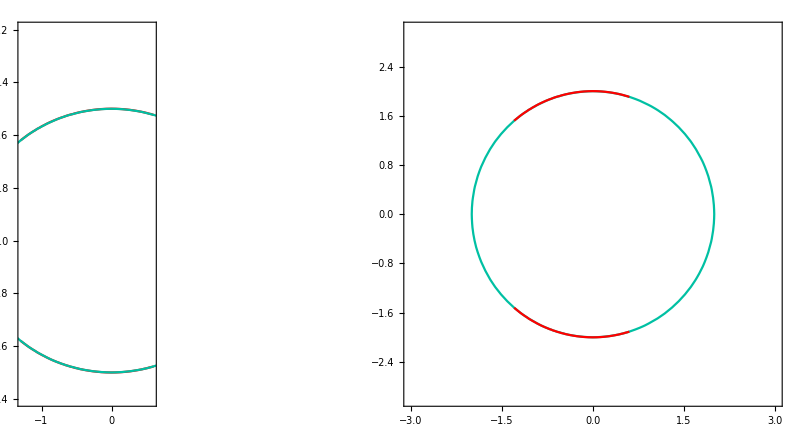

```mathematica
(* 1. 有bug *)
fp11 = Show[fp1, fp2];

(* 2. 正常 *)
fp12 = Show[fp2, fp1];

GraphicsRow[{fp11,,,,,fp12}, Spacings->Automatic]
(* 使用,来增加间距 *)
```

备注： 出现Bug，是应为Show的时候，默认是把第二幅图放到第一幅图中，所以我们要把范围大的图放在前面

### 设置刻度

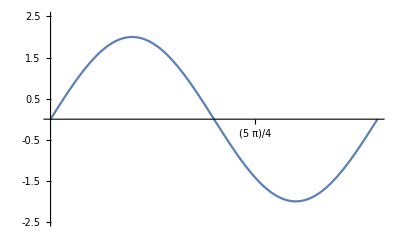

```mathematica
Plot[2*Sin[x], {x, 0, 2*Pi}, PlotRange->{-2.5, 2.5}, Ticks->{Range[-4Pi, 4Pi, Pi/4], Range[-2.5, 2.5, 0.5]}]
```

### 照明, 背景， 纹理等选项

```mathematica
SphericalPlot3D[1 + Sin[5*ϕ]*Sin[10*θ]/10, 
	{θ, 0, Pi}, {ϕ, 0, 2*Pi},
	Axes->False,
	Background->Black,
	Boxed->False,
	Lighting->"Standard",
	PlotStyle->Texture[-Graphics-]
]
```

-Graphics3D-

### 定义一个用于绘图的函数

```mathematica
plotfun[fun_, xlimits_, ylimits_] := ContourPlot[fun, 
	xlimits, ylimits,
	ContourStyle->{
		RGBColor["#00C0A3"], 
		Thickness[0.004]
	},
	AspectRatio->((xlimits[[2]]//Abs) + (xlimits[[3]]//Abs))/((ylimits[[2]]//Abs) + (ylimits[[3]]//Abs)), 
	AxesOrigin->{0,0}, 
	Axes->True,
	Frame->False,
	AxesStyle->Arrowheads[{0, 0.03}],
	(* 0 -> 在正半轴； 1-> 同时在正负半轴*)
	(* 0.03 -> 箭头的大小 *)
	AxesLabel->{"x", "y"}
]
```

### 绘图函数使用方法

原始绘制方法

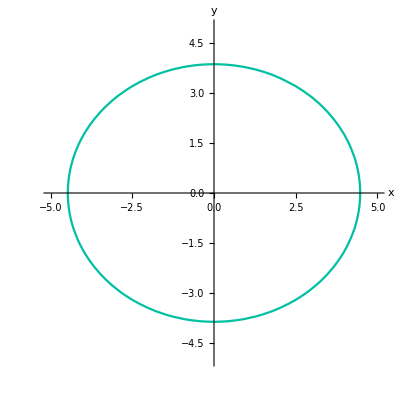

```mathematica
ContourPlot[
	x^2/4 + y^2/3 == 5, {x, -5, 5}, {y, -5, 5},
	ContourStyle->{
		RGBColor["#00C0A3"], 
		Thickness[0.004]
	},
	AspectRatio->1, 
	AxesOrigin->{0,0}, 
	Axes->True,
	Frame->False,
	AxesStyle->Arrowheads[{0, 0.03}],
	(* 0 -> 在正半轴； 1-> 同时在正负半轴*)
	(* 0.03 -> 箭头的大小 *)
	AxesLabel->{"x", "y"}
]
```

```mathematica
Plot3D[x*y + 2*x, {x, -5, 5}, {y, -5, 5}]
```

-Graphics3D-

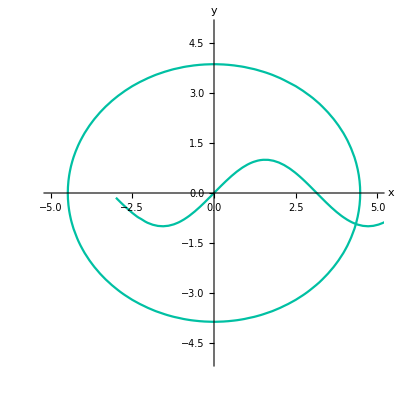

```mathematica
xlimits = {x, -3, 6};
ylimits = {y, -4, 5};
fp31 = plotfun[y==Sin[x], xlimits, ylimits];
fp32 = plotfun[x^2/4 + y^2/3 == 5, {x, -5, 5}, {y, -5, 5}];

Show[fp32, fp31]
```

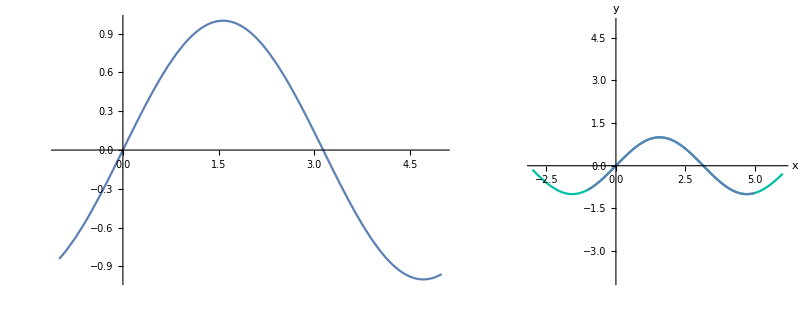

```mathematica
fp33 = Plot[Sin[x], {x, -1, 5}];

GraphicsRow[{fp33, Show[fp31, fp33]}]
```

```mathematica
Plot3D[x^2 + y^2 - 4, 
	{x, -3, 3}, {y, -3, 3},
	AxesOrigin->{0, 0, 0},
	Axes->True,
	Boxed->False,
	AxesLabel->{"x", "y", "z"},
	ColorFunction->"Rainbow",
	(*AxesStyle->{{Thick}, {Thick}, {Thick}}*)
	AxesStyle->Arrowheads[0, 0, 0.03]
]
```

-Graphics3D-

绘制箭头
1. 第一个参数 ArrowHead 表示箭头的大小
2. 第二个表示 箭头的起始位置

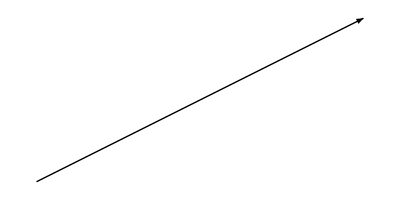

```mathematica
(* 第一种：平面 *)
arrow1 = {Arrowheads[0.05], Arrow[{{0,0}, {2, 1}}]}//Graphics;

(* 第二种：三维空间 *)
arrow2 = {Arrowheads[.1], 
	Arrow[Tube[
		{{0,0,0}, {2,1,1}}
		]]
}//Graphics3D;


(* 第三种： 双头箭头*)
arrow3 = {Arrowheads[{-.1, .1}],
	Arrow[Tube[
		BSplineCurve[
		{{0,0,0}, {.2,1,0.5},{2,1,1}}
		]]]
}//Graphics3D;

GraphicsRow[{arrow1, arrow2, arrow3}]
```

```mathematica
RGBColor["#00C0A3"]

RGBColor["#00C0A3"] /. RGBColor[r_, g_, b_] :> {r, g, b}
RGBColor[0.,0.7529411764705882,0.6392156862745098]
```

RGBColor[0., 0.7529411764705882, 0.6392156862745098]

{0.,0.752941,0.639216}

RGBColor[0., 0.7529411764705882, 0.6392156862745098]

## 三维坐标轴建立

```mathematica
(* 1. 定义一个产生箭头的命令 *)
(*arrow[start_, end_] := 
Graphics3D[
	{Arrowheads[.02], 
		Arrow[Tube[{start, end}, 0.05]]
	},
	Boxed->False
];*)

arrow[start_, end_, type_] := 
Graphics3D[
	{type, 
		{ Arrowheads[.02], Arrow[Tube[{start, end}, 0.06]] }	
	}, 
Boxed->False];


(* 2. 创建三个坐标轴的箭头, 使用颜色进行区分 *)
xaxis = arrow[{-10, 0, 0}, {10, 0, 0}, Blue];
yaxis = arrow[{0, -10, 0}, {0, 10, 0}, Green];
zaxis = arrow[{0, 0, -10}, {0, 0, 10}, Red];


(* 3. 展示在同意坐标轴 *)
axis = {xaxis, yaxis, zaxis};
(*Table[Graphics3D[{c, CapForm[None], JoinForm[None],l}],{c,{Red,Green,Blue,Yellow}}]*)


(* 4. 绘制一个函数由于测试 *)
fp4 = Plot3D[0.4*x + 0.2*Sin[y] + 0.2*x*y, {x, -5, 7}, {y, -6, 4}, ColorFunction->"Rainbow"];


(* 5. 显示三维函数图像和坐标轴 *)
Show[axis, fp4]
```

-Graphics3D-

## 颜色函数

```mathematica
colorfun = Function[{x,y,z}, Hue[z]];
```

```mathematica
colorfun[1, 2, 1]
colorfun[2, 2, 0.1]
colorfun[-1, 2, 0.1]
```

Hue[1]

Hue[0.1]

Hue[0.1]

### 一个技巧：使用颜色去作用任何对象的方法

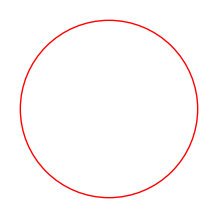

```mathematica
{Hue[1], Circle[{0, 0}, 1]}//Graphics
```

```mathematica
Style[Sqrt[Sin[x]/x]//TraditionalForm, Blue]
```

√((sin(x))/x)

### 生成一个颜色渐变列表

```mathematica
colorgra = ColorData[#,"Image"]&/@ColorData["Gradients"];
```

### 自定义颜色渐变

```mathematica
fp5 = Plot3D[0.4*x + 0.2*Sin[y] + 0.2*x*y, {x, -5, 7}, {y, -6, 4}, 
	ColorFunction->{RGBColor["#2F4858"], RGBColor["#199190"], RGBColor["#5EC290"]}];
	
Show[axis, fp5]
```

-Graphics3D-

## 矢量绘制

### 普通箭头绘制

```mathematica
fp71 = NumberLinePlot[x>-1, {x, -4.3, 5}];
fp72 = NumberLinePlot[x>=-2, {x, -4, 2}];

GraphicsRow[{fp71, fp72}]
(* 需要手动放大一下 *)
```

-Graphics-

可以使用 Interval 来指定区间

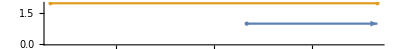

```mathematica
NumberLinePlot[
	{Interval[{5, Infinity}], Interval[{2, 7}]}, 
	AxesStyle->Arrowheads[{0, 0.03}]
]
```

也可以是散点绘制

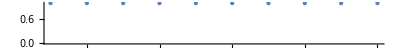

```mathematica
NumberLinePlot[Table[i, {i, 1, 10}], AxesStyle->Arrowheads[{0, 0.03}]]
```

### 绘制向量场

本质上就是给每一个坐标点 (x, y)指定一个方向，这个方向就是向量，

比如下面我们规定每一个点 (x, y) 的方向为: (1, x^2)
实际上就是微分方程：dy/dx=x^2 的向量场

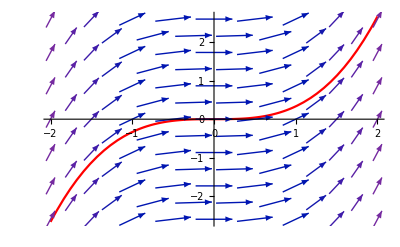

```mathematica
fvec = VectorPlot[{1, x^2}, {x, -4, 4}, {y, -4, 4}, AxesOrigin->{0, 0}, Axes->False, Frame->False];

fp6 = Plot[1/3*x^3, {x, -2, 2}, PlotStyle->Red,  AxesStyle->Arrowheads[{0, 0.03}] ];
Show[fp6, fvec]
```

类似的命令还有 StreamPlot

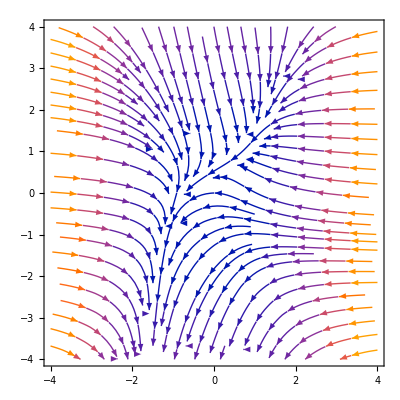

```mathematica
StreamPlot[{-1-x^3+y, x-y^2},  {x, -4, 4}, {y, -4, 4}]
```

### 三维场的绘制

```mathematica
VectorPlot3D[{x, y, z}, {x, -1, 1}, {y, -1, 1}, {z,-1, 1},PlotTheme->"Classic"]
```

-Graphics3D-

## 散点图绘制

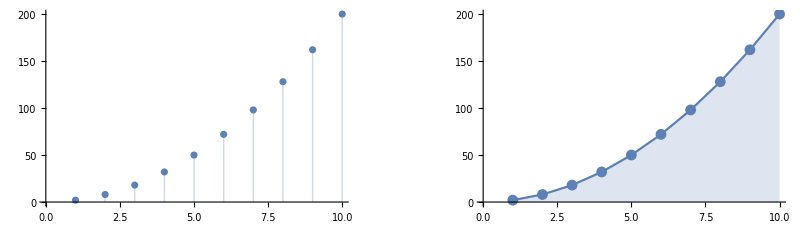

```mathematica
fp81 = ListPlot[Table[2*i^2, {i, 1, 10}], Filling->Axis];
fp82 = ListLinePlot[Table[2*i^2, {i, 1, 10}], Filling->Axis, Mesh->All];

GraphicsRow[{fp81,,fp82}]
```

备注： 三维空间的网格绘制在二维空间就是线段的绘制了

## 可视化矩阵

1. 较深的地方数值较大
2. 冷色表示负值，如蓝色，以暖色表示正值，如桔色.值的幅值越大，相应位置的颜色就越浓.

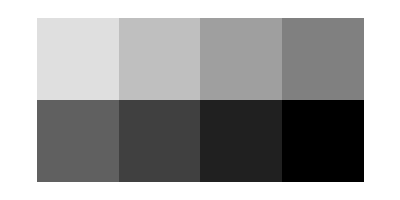

```mathematica
ArrayPlot[{{1, 2, 3, 4}, {5,6,7,8}}]
```

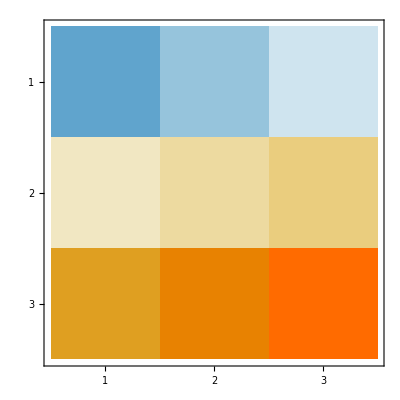

```mathematica
MatrixPlot[{{-10,-5,-1}, {2,4,6}, {20,30,40}}]
```

## 平面区域绘制

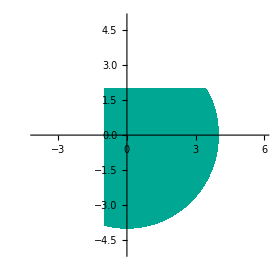

```mathematica
RegionPlot[{x^2+y^2<16 && x+y<8 && x>-1 && y<2}, 
	{x, -4, 6}, {y, -5, 5}, 
	PlotStyle->RGBColor["#00A894"],
	BoundaryStyle->None,
	Axes->True,
	Frame->False,
	AxesOrigin->{0, 0},
	AspectRatio->1
]
```

### Hamilton 图

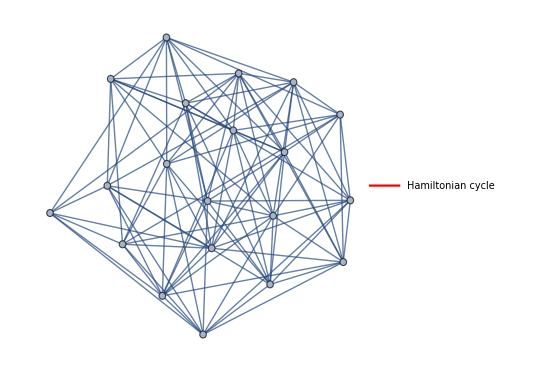

```mathematica
g=RandomGraph[{20,100}];
h=FindHamiltonianCycle[g];
Legended[HighlightGraph[g,Style[h,Directive[Thick,Red]]],LineLegend[{Directive[Thick,Red]},{"Hamiltonian cycle"}]]
```

## 用图表来可视化数据

```mathematica
BarChart[RandomInteger[{1, 300}, 40], PlotTheme->"Detailed"]
```

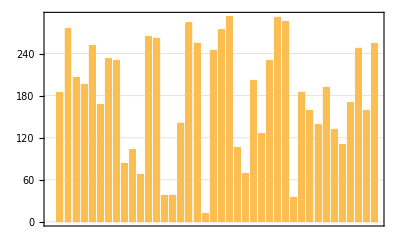

```mathematica
Flatten[Table[{i, j}, {i, 1, 4}, {j, 1, 3}], 1]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3},{4,1},{4,2},{4,3}}

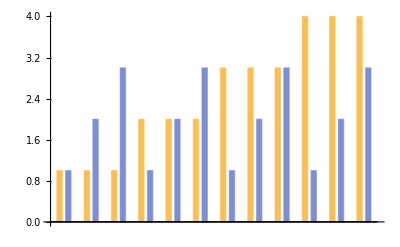

```mathematica
BarChart[Flatten[Table[{i, j}, {i, 1, 4}, {j, 1, 3}], 1]]
```

## 总结

我们提供了各种二维图形基元:

点、线、箭头、多边形、圆盘、圆圆、矩形、连接曲，线、实心曲线、样条曲线、兰角形 等等.

这些基元通常使用一组坐标作为参数，取决于你所使用的特定基元，还有一些另外的参数.
有些基元可以不使用任何参数，在这种情况下 Mathematica 将假定必须的坐标为 (0 ， 0).

### Disk 圆盘

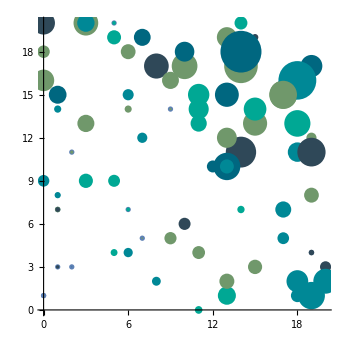

```mathematica
num = 80;
xls = RandomInteger[{0, 20}, num];
yls = RandomInteger[{0, 20}, num];

xycoor = {xls, yls}//Transpose;
color = {RGBColor["#00A894"], RGBColor["#008896"], RGBColor["#006780"], RGBColor["#2F4858"], RGBColor["#70986B"]};

disks = Table[
	 Graphics[{color[[RandomInteger[{1, 5}]]], Disk[xycoor[[i]], RandomReal[{0, 0.05}]*#1+RandomReal[{0, 0.05}]*#2&[xycoor[[i]][[1]], xycoor[[i]][[2]]]]}],
	(*Graphics[{Hue[RandomReal[{0, 1}]], Disk[xycoor[[i]], RandomReal[{0, 0.05}]*#1+RandomReal[{0, 0.03}]*#2&[xycoor[[i]][[1]], xycoor[[i]][[2]]]]}],*)
	{i, 1, num}
];
fp91 = disks;
fp92 = ListPlot[xycoor, AspectRatio->(Max[yls])/(Max[xls])];
Show[fp92, fp91]
```

### 矩形

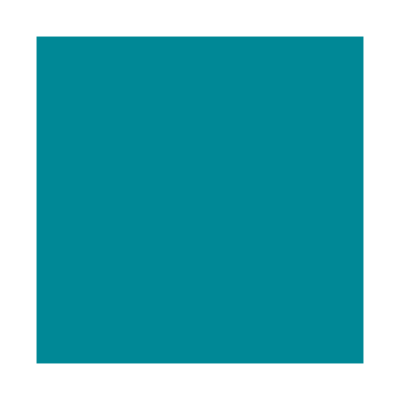

```mathematica
Graphics[{color[[2]], Rectangle[{0, 0}, {1, 1}]}]
```

### 三维图形的渲染

```mathematica
Graphics3D[{
	Blue, Opacity[0.5], Sphere[{0.5, 0.5, 0}, 0.5], 
	Blue, Opacity[0.5], Sphere[{-0.5, -0.5, 0}, 0.5],
	Blue, Opacity[0.5], Sphere[{0.5, -0.5, 0}, 0.5], 
	Blue, Opacity[0.5], Sphere[{-0.5, 0.5, 0}, 0.5],
	Blue, Opacity[0.5], Sphere[{0, 0, 0.5}, 0.5], 
	Blue, Opacity[0.5], Sphere[{0, 0, -0.5}, 0.5],
	Green,Sphere[{0,0,0}, 0.75]
	},
	Boxed->False	
]
```

-Graphics3D-